```mathematica
(* Perturbation attempt on 
x + lambda * q * x^(q - 1) = b 
by
epsilon * x + lambda * q * x^(q - 1) = b
*)
Clear["Global`*"]
S[ϵ_,nmax_]:=If[nmax==Infinity,Sum[a[n]*ϵ^n,{n,1,nmax}],Sum[a[n]*ϵ^n,{n,1,nmax}]+O[ϵ]^(nmax+1)]
Sk[ϵ_,nmax_,k_]:=S[ϵ,nmax]^k

(* coef a[0] (i.e. x(epsilon) when epsilon = 0) *)
ω[b_,q_,λ_]:=(b/(λ*q))^(1/(q - 1))
(* x^(q-1) *)
xqm1[ϵ_,b_,q_,λ_,nmax_,kmax_]:= Sum[Binomial[q-1,k]/k!*ω[b,q,λ]^(q-1-k)*Sk[ϵ,nmax,k],{k,0,kmax}]

eqn[ϵ_,b_,q_,λ_,nmax_,kmax_]:=ϵ*(ω[b,q,λ] + S[ϵ,nmax])+λ*q*xqm1[ϵ,b,q,λ,nmax,kmax]-b

kmx=3; (* inner sum index *)
nmx=3; (* outer sum index *)
eqn2=Simplify[eqn[ϵ,b,q,λ,nmx,kmx],Assumptions->Infinity>λ>0&&Infinity>b>0&&1>q>0];

(* Remove higher order terms O[epsilon]^(nmx + 1)*)
eqn3=Normal[eqn2];

(* Extract coefficients *)
coefs=CoefficientList[Collect[eqn3,ϵ],ϵ];
coefssol = Solve[coefs==0,Table[a[n],{n,1,Length[coefs]-1}]];
Table[a[n],{n,1,3}]/.coefssol[[1]]
x[B_,Q_,Λ_]:=ω[B,Q,Λ]+Total[Table[a[n],{n,1,Length[coefs]-1}]/.coefssol[[1]]/.{b->B,q->Q,λ->Λ}]

err[b_,q_,λ_]:=N[(Simplify[x[b,q,λ]+λ*q*x[b,q,λ]^(q-1)])/b]
```

{-(b/(q λ))^(3/(-1+q)-q/(-1+q))/((-1+q) q λ),-((-6+q) (b/(q λ))^(5/(-1+q)-(2 q)/(-1+q)))/(4 (-1+q)^2 q^2 λ^2),-((204-80 q+7 q^2) (b/(q λ))^(7/(-1+q)-(3 q)/(-1+q)))/(72 (-1+q)^3 q^3 λ^3)}

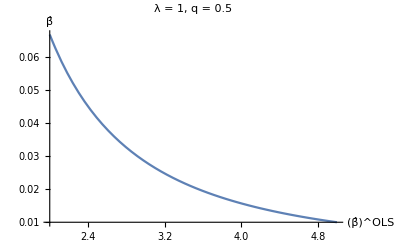

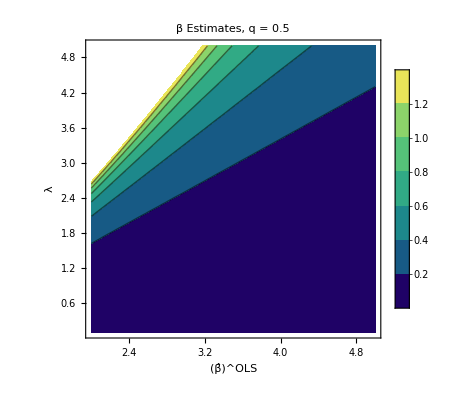

-Graphics3D-

1.21782

11/(128 b^8)+1/(8 b^5)+1/(4 b^2)

{{a[1]→-(b/(q λ))^(3/(-1+q)-q/(-1+q))/((-1+q) q λ),a[2]→-((-6+q) (b/(q λ))^(5/(-1+q)-(2 q)/(-1+q)))/(4 (-1+q)^2 q^2 λ^2)}}

```mathematica
bmin=2; bmax=5;
lmin=0.1; lmax=5;
Clear[b,q,λ]
q=1/2;
λ=1;
Plot[x[b,q,λ],{b,bmin,bmax},
AxesLabel->{Superscript[OverHat[β],"OLS"],OverHat[β]},
PlotLabel->StringJoin["λ = ",ToString[λ], ", q = ", ToString[N[q]]]]

Clear[b,q,λ]
q=1/2;
ContourPlot[x[b,q,λ],{b,bmin,bmax},{λ,lmin,lmax},
FrameLabel->{Superscript[OverHat[β],"OLS"],λ},
PlotLabel->StringJoin[ToString[β]," Estimates, q = ", ToString[N[q]]],
PlotLegends->Automatic,
ColorFunction->ColorData["BlueGreenYellow"]]

Clear[b,q,λ]
q=1/2;
Plot3D[x[b,q,λ],{b,bmin,bmax},{λ,lmin,lmax},
AxesLabel->{Superscript[OverHat[β],"OLS"],λ},
PlotLabel->StringJoin[ToString[β]," Estimates, q = ", ToString[N[q]]],
ColorFunction->ColorData["BlueGreenYellow"]]
```

```mathematica
{a[1]->1/8,a[2]->11/128,a[3]->221/3072}/.Rule->List
```

{{a[1],1/8},{a[2],11/128},{a[3],221/3072}}